1. naloga

```mathematica
ClearAll
```

ClearAll

```mathematica
d =Daljica[{-1, 1}, {3, -1}]
d2 = Daljica[{-1, -1},{3, 1}]
d3 = Daljica[{-1, 2},{3, 0}]
```

{{-1,1},{3,-1}}[{-1,1},{3,-1}]

{{-1,1},{3,-1}}[{-1,-1},{3,1}]

{{-1,1},{3,-1}}[{-1,2},{3,0}]

```mathematica
Dolzina[Daljica[AA_, BB_]] := Norm[BB - AA]
Dolzina[d]
```

2 √5

```mathematica
Slika[Daljica[AA_, BB_]] := Line[{AA, BB}]
```

```mathematica
Slika[d]
```

Line[{{-1,1},{3,-1}}]

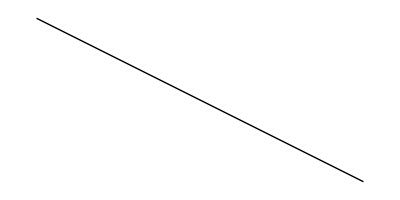

```mathematica
Narisi[d_Daljica] := Graphics[Slika[d]]
Narisi[d]
```

```mathematica
ClearAll[x, y]
```

```mathematica
EnacbaNosilke[Daljica[AA_,BB_]] := Module[{x1, x2, y1, y2, k, n},
{x1, y1} = AA;
{x2, y2} = BB;
k = (y2 -y1)/(x2 - x1);
n = n /.First[Solve[y1 == k * x1 +n, n]];
y == k * x +n
]
```

```mathematica
EnacbaNosilke[d]
```

y==1/2-x/2

2. Naloga

```mathematica
Presek[Daljica[AA_, BB_], Daljica[CC_,DD_]] := Module[{resitev},
resitev = Solve[{AA + r (BB - AA)==CC+s(DD-CC), 0≤r, r ≤ 1, 0≤ s, s≤1},{s,r}];
]
```

```mathematica
Presek[d, d2]
```

```mathematica
Presek[d, d3]
```